```mathematica
mn = 0.939;
TT = 10^10*3.154*^7/6.58*^-25;
```

```mathematica
qp[q0_, Ek_, mx_] := √(2Ek mx) + √(2mx(Ek - q0));
qm[q0_, Ek_, mx_] := √(2Ek mx) - √(2mx(Ek - q0));
vr[Ek_, mx_]:= (mn +mx)/(mn mx)√(2mx Ek);
vperp[q_,Ek_,mx_]:= vr[Ek, mx] + (q(mx + mn))/(2(mx*mn));
prefactor[Ek_, mx_]:= 1/(64 π^3 mx √(2mx Ek));
```

## Matrix Elements

```mathematica
MC[q_,Ek_,mx_]:=16 mx^2 mn^2;
Mq2[q_,Ek_,mx_]:= vperp[q, Ek, mx];

D1[q_,Ek_,mx_]:=MC[q,Ek,mx];
D2[q_,Ek_,mx_]:= 4 mn^2 q^2;
D3[q_,Ek_,mx_]:=4 mx^2 q^2;
D4[q_,Ek_,mx_]:= q^4;
D5[q_,Ek_,mx_]:= MC[q,Ek,mx];
D6[q_,Ek_,mx_]:= 8 mx^2*(mn^2*vperp[q, Ek, mx]^2+4 q^2);
D7[q_,Ek_,mx_]:=8 mn^2*(mx^2*vperp[q, Ek, mx]^2+4 q^2);
D8[q_,Ek_,mx_]:=12 mx^2 mn^2;
D9[q_,Ek_,mx_]:=3 mx^2 mn^2;
```

## Interaction Rate

```mathematica
Γ[Ek_, M2_,mx_]:= prefactor[Ek, mx]*Integrate[q0*M2[q, Ek, mx],{q0, 0, Ek}, {q, qm [q0, Ek, mx], qp[q0, Ek, mx]}];
```

## Therm Time

```mathematica
denom[Ek_, M2_,mx_]:= prefactor[Ek, mx]*Integrate[q0^2*M2[q, Ek, mx],{q0, 0, Ek}, {q, qm [q0, Ek, mx], qp[q0, Ek, mx]}];
fracLost[Ek_, M2_,mx_]:=denom[Ek, M2, mx]/Γ[Ek, M2, mx];
```

```mathematica
ttnoΛ[E0_, Eth_,M2_, mx_]:=-Integrate[1/denom[Ek, M2, mx], {Ek, E0, Eth},GenerateConditions->False];
```

## Summation Therm

```mathematica
τ[E0_,M2_,mx_]:= (
Clear[Enow, time];
Enow = E0;
time =0;
While[ Enow > 8*^-9,
time +=1/Γ[Enow, M2, mx];
Enow += -fracLost[Enow, M2, mx];
];
Return[time];
Clear[Enow, time];
)
```

## Λ constraints

```mathematica
Λ[M2_, T_, mx_]:= (TT/ttnoΛ[mx/3,T,M2, mx])^0.25;
```

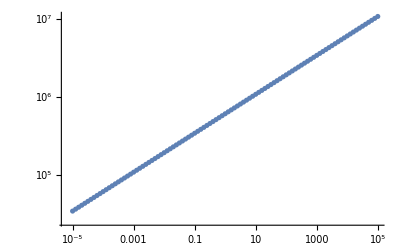

```mathematica
ListLogLogPlot[{With[{x:=10^xp}, ParallelTable[{x, Λ[D1, 8*^-9,x]}, {xp, -5, 5, 0.1}]]}] (* above = not thermalised, below = thermalised*)
```

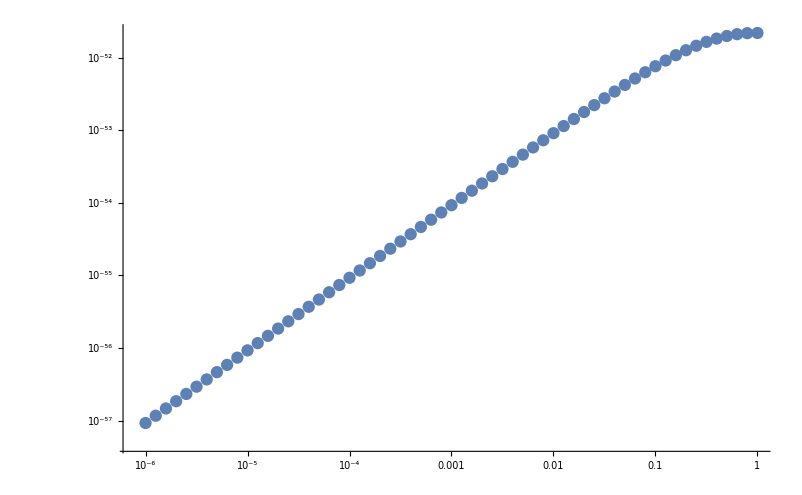

```mathematica
ListLogLogPlot[{With[{x:=10^xp}, ParallelTable[{x, ((0.197*^-13)^2)/(π Λ[MC,8*^-9, x]^4)*(x^2 mn^2)/(x+mn)^2}, {xp, -6, 0, 0.1}]]}]
```